# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"M","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) l’Hospital

lim_(x→0) (ⅇ^x-sin(x)-1)/x^2=?

a) Calculate the limit above using l’Hospitalsche Regel
b) Calculate the limit above using the Taylor expansion

#### Useful formulas

Regel von de l’Hospital

If ∃ lim_(x→x_0) (f'(x))/(g'(x))  ∧   lim_(x→x_0) f(x)=0  ∧  lim_(x→x_0) g(x)=0  ∧  g'(x)≠0, then:

lim_(x→x_0) (f(x))/(g(x))=lim_(x→x_0) (f'(x))/(g'(x))

Taylor’sche Formel

f(x)=(T_n f)(x; a)+R_(n+1)(x;a)

(T_n f)(x;a)=∑_(k=0)^n (f^(k)(a))/(k!)(x-a)^k

R_(n+1)(x;a)=1/(n!)∫_a^x (x-t)^n f^(n+1)(t)ⅆt

## Solution

## a)

lim_(x→0) (ⅇ^x-sin(x)-1)/x^2=lim_(x→0) (ⅇ^x-cos(x))/(2x)=lim_(x→0) (ⅇ^x+ sin(x))/2=(ⅇ^0+ sin(0))/2=1/2

We used the l’Hospitalsche Regel in the first and second equality. We also have to check that all assumptions of the Regel are satisfied, such as lim_(x→0) (ⅇ^x-sin(x)-1)=0 etc.

## b)

ⅇ^x=1+x+x^2/2+O(x^3)
sin(x)=x+O(x^3)

ⅇ^x-sin(x)-1=(1+x+x^2/2)-(x)-1+O(x^3)=x^2/2+O(x^3)

lim_(n→0) (ⅇ^x-sin(x)-1)/x^2=lim_(n→0) (x^2/2+O(x^3))/x^2=lim_(n→0) (1/2+(O(x^3))/x^2)

Because lim_(x→0) Abs[(O(x^3))/x^2]≤lim_(x→0) Abs[(C x^3)/x^2]=Abs[C]lim_(x→0) Abs[x]=Abs[C]·0=0 as follows from the properties of O, we have: lim_(x→0) (O(x^3))/x^2=0. Therefore:

lim_(n→0) (ⅇ^x-sin(x)-1)/x^2=lim_(n→0) (1/2+(O(x^3))/x^2)=1/2

# 2) Ableitung

f: ℝ→ℝ

f(x)=Piecewise[{{x^2 sin(1/x), x≠0}, {0, x=0}}]

a) f'(x)=?   for x≠0

b) Optimale lineare Näherung L + Ableitung for x=0

#### Useful formulas

Ableitung of a composite function (Satz 11.3)

(g ◦ f)'(x)=g'(f(x))·f'(x)

Lineare Approximation (Satz 11.1)

Sei f:D→ℝ differenzierbar in x_0∈D⊂ℝ. Dann gilt:

f(x_0+h)=f(x_0)+f'(x_0)h+o(h),  h→0

## Plots

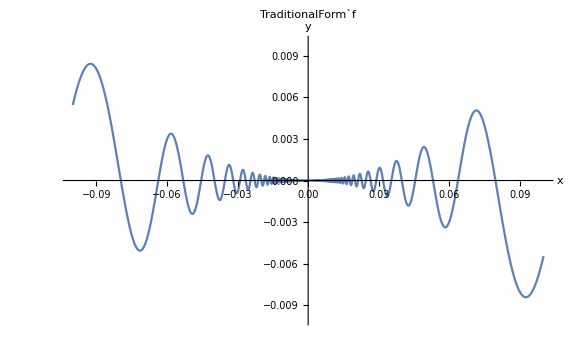

```mathematica
plotFun[x^2 Sin[1/x],{{-.1,.1},{-.01,.01}},{},"TraditionalForm`f"]
```

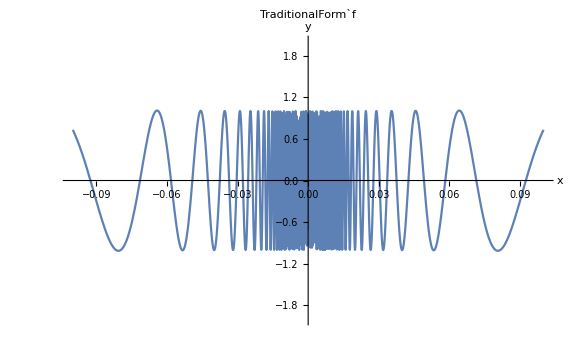

```mathematica
plotFun[D[x^2 Sin[1/x],x],{{-.1,.1},{-2,2}},{},"TraditionalForm`f"]
```

## Solution

## a)

f'(x)=(x^2 sin(1/x))'=2 x sin(1/x)+x^2 cos(1/x)-1/x^2=2 x sin(1/x)-cos(1/x)

## b)

f'(0)=lim_(x→0) (f(x) - f(0))/(x - 0)=lim_(x→0) (x^2 sin(1/x))/x=lim_(x→0) x sin(1/x)

Also:

Abs[x sin(1/x)]≤Abs[x]  ⇒   lim_(x→0) Abs[x sin(1/x)]≤  lim_(x↘0) Abs[x]=0

Therefore:

f'(0)=lim_(x→0) x sin(1/x)=0

and we can conclude that f is at x=0 differenzierbar with f'(0)=0. Function f does not have stetige Ableitung at x=0, so we cannot use the Taylor expansion. But, we can use formula

f(x_0+h)=f(x_0)+f'(x_0)h+o(h)   with   x_0=0   to get:

f(h)=f(0)+f'(0)h+o(h)=0+0·h+o(h)=0+o(h) for h→0

The optimale lineare Näherung L(x)=f(x_0)+c(x-x_0) for x_0=0 then reads

L(x)=0

In other words, function f behaves in the vicinity of zero as a zero function.

# 3) Taylorreihe

f(x)=ln(1+x)
g(x)=ln(1+x^2)

a) Taylorreihe of f at x=0

b) calculate using the definition of an Ableitung

#### Useful formulas

Taylorreihe

(T f)(x;a)=∑_(k=0)^∞ (f^(k)(a))/(k!)(x-a)^k

Eindeutigkeitssatz (Satz 11.10)

f(x)=∑_(k=0)^∞ (a_k(x-a))^k   ⇒   (T f)(x;a) = f(x)

## Solution

## a)

f(0)=ln(1+x)|_(x=0)=ln(1+0)=0

f'(0)=(1/(1+x))|_(x=0)=1

f''(0)=(-1/(1+x)^2)|_(x=0)=-1

f'''(0)=(((-1)(-2))/(1+x)^3)|_(x=0)=(-1)(-2)=2

We can guess (and prove by mathematical induction) that for the k-th Ableitung we get:

f^(k)(0)=(-1)^(k-1)(k-1)!   for  k≥1

Then:

(T f)(x;0)=∑_(k=0)^∞ (f^(k)(0))/(k!)(x-0)^k=f^(0)(0)+∑_(k=1)^∞ (f^(k)(0))/(k!)x^k=0+∑_(k=1)^∞ ((-1)^(k-1)(k-1)!)/(k!)x^k=∑_(k=1)^∞ (-1)^(k-1)/k x^k

## b)

Let us just plug x^2 into the Taylorreihe for f. We get:

g(x)=ln(1+x^2)=f(x^2)=∑_(k=1)^∞ (-1)^(k-1)/k x^(2k)

From the Eindeutigkeitssatz therefore:

(T g)(x;0)= ∑_(k=1)^∞ (-1)^(k-1)/k x^(2k)

# 4) Taylor-Polynom

f(x)=x^2-3x+1
a=1

a) (T_2 f)(x;a)=f(x)?

b) f(x)=∑_(k=0)^n c_k x^k  ⇒  f(x)=(T_n f)(x;a) ?

#### Useful formulas

Taylor-Polynom der Ordnung n von f um a

(T_n f)(x;a)=∑_(k=0)^n (f^(k)(a))/(k!)(x-a)^k

Taylor’sche Formel

f(x)=(T_n f)(x; a)+R_(n+1)(x;a)

R_(n+1)(x;a)=1/(n!)∫_a^x (x-t)^n f^(n+1)(t)ⅆt

## Solution

## a)

(T_2 f)(x;1)=f(1)+f'(1)(x-1)+(f''(1))/2(x-1)^2=(x^2-3x+1)|_(x=1)+ (2x-3)|_(x=1)(x-1)+1/2(2)|_(x=1)(x-1)^2=(-1)+ (-1)(x-1)+(x-1)^2=-x+(x-1)^2=x^2-3x+1=f(x)

## b)

We can use the Eindeutigkeitssatz to observe that for polynomial f the Taylorreihe is actually a polynomial and this polynomial is identical to f. The second option is to use for instance the Taylor’sche Formel and show that R_(n+1)(x;a)=0 in the following way:

Function f is a polynomial of degree n: f(x)=∑_(k=0)^n c_k x^k. It implies that its (n+1)-th Ableitung gives a zero function, i.e. f^(n+1)(x)=0. We have:

R_(n+1)(x;a)=1/(n!)∫_a^x (x-t)^n f^(n+1)(t)ⅆt=1/(n!)∫_a^x (x-t)^n·0ⅆt=0

# 5) Null

g(x)=exp(-1/x^2)

a) g'(x)=?   x≠0
     g''(x)=?  x≠0

b) lim_(x→0) g'(x)=0  ?
     lim_(x→0) g''(x)=0 ?

c) lim_(x→0) g^(k)(x)=0 ? (Holiday challenge)

## Plots

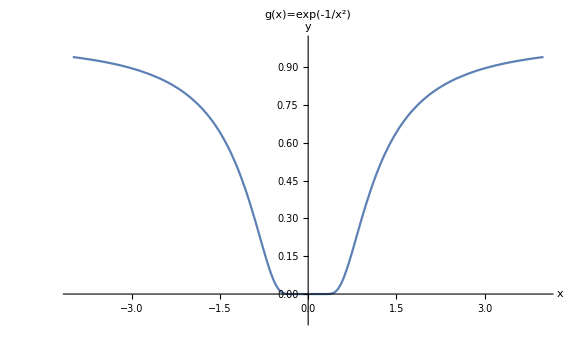

```mathematica
plotFun[Exp[-1/x^2],{{-4,4},{-.1,1}},{},"g(x)=exp(-1/x^2)"]
```

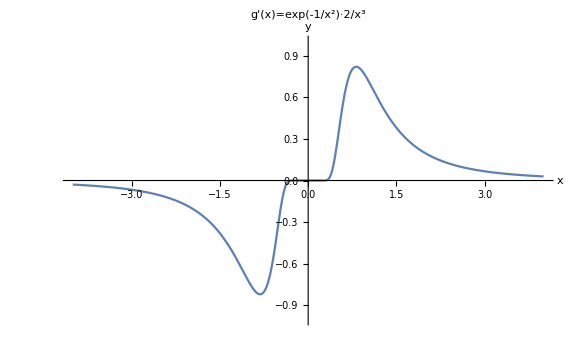

```mathematica
plotFun[exp(-1/x^2)2/x^3,{{-4,4},{-1,1}},{},"g'(x)=exp(-1/x^2)·2/x^3"]
```

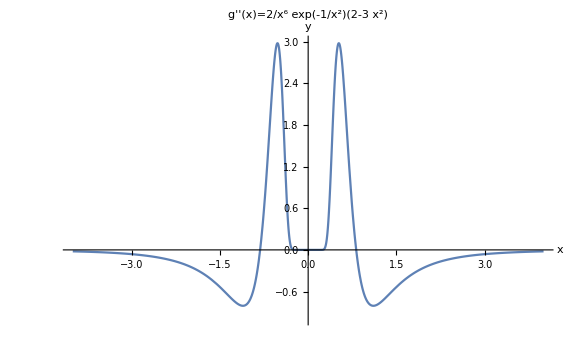

```mathematica
plotFun[2/x^6 exp(-1/x^2)(2-3 x^2),{{-4,4},{-1,3}},{},"g''(x)=2/x^6 exp(-1/x^2)(2-3 x^2)"]
```

## Solution

## a)

g'(x)=exp(-1/x^2)·2/x^3
g''(x)=(exp(-1/x^2)·2/x^3)'=(exp(-1/x^2)·2/x^3)2/x^3+exp(-1/x^2)((2(-3))/x^4)=2/x^6 exp(-1/x^2)(2-3 x^2)

## b)

We make a substitution y=1/x:

lim_(x→0) g'(x)=lim_(x→0) exp(-1/x^2)·2/x^3=2·lim_(y→∞) exp(-y^2)·y^3=2·lim_(y→∞) y^3/(exp(y^2))
lim_(x→0) g''(x)=lim_(x→0) 2/x^6 exp(-1/x^2)(2-3 x^2)=2·lim_(y→∞) y^6 exp(-y^2)(2-3/y^2)=4·lim_(y→∞) (y^6/(exp(y^2)))-6·lim_(y→∞) (y^4/(exp(y^2)))

Hint: “Die Exponentialfunktion gewinnt immer gegenuber Polynomfunktionen.” That is:

lim_(y→∞) y^m/(exp(y^2))=0 for all m∈ℤ

Therefore:

lim_(x→0) g'(x)=2·lim_(y→∞) y^3/(exp(y^2))=0

lim_(x→0) g''(x)=4·lim_(y→∞) (y^6/(exp(y^2)))-6·lim_(y→∞) (y^4/(exp(y^2)))=0

## c)

It can be shown by mathematical induction that the k-th Ableitung of g is of the form:

g^(k)(x)=exp(-1/x^2)(P(x))/x^m, where m∈ℤ and P is a polynomial P(x)=∑_(q=0)^n c_q x^q. Thus:

lim_(x→0) g^(k)(x)=lim_(x→0) exp(-1/x^2)1/x^m(∑_(q=0)^n c_q x^q)=∑_(q=0)^n c_q·lim_(x→0) exp(-1/x^2)1/x^(m-q)=∑_(q=0)^n c_q·lim_(y→∞) y^(m-q)/(exp(y^2))

Using the Hint from b) we see that all limits in the sum are zero, the sum is therefore also zero. We get:

lim_(x→0) g^(k)(x)=0  for all k≥1

The Taylorreihe of g is thus identically zero function!